## Preliminaries

Formulas for the transition times

```mathematica
R0 = 2;
Rc = 4/3;

Imax = 0.01;

μf = Imax + (Log[R0]+1)/R0;

μ[Is_,S_]:=Is-1/R0 Log[S]+S
ν[Is_,S_]:=Is-1/Rc Log[S]+S

T0[ν1_,μ1_,ν0_,μ0_]:=NIntegrate[1/(R0/Rc μ0-v-(R0-Rc)/Rc Exp[(R0 Rc)/(R0-Rc)(μ0-v)]),{v,ν0,ν1}]

Tc[ν1_,μ1_,ν0_,μ0_]:=NIntegrate[1/(-μ+Rc/R0 ν1+(R0-Rc)/R0 Exp[(R0 Rc)/(R0-Rc)(μ-ν1)]),{μ,μ0,μ1}]

T[ν_,μf_,ν0_,μ0_]:=T0[ν,μ0,ν0,μ0]+Tc[ν,μf,ν,μ0]

(*T0[1.5,1.2,ν0,μ0]
Tc[1.5,1.2,ν0,μ0]
T[1.5,1.2,ν0,μ0]*)
```

```mathematica
μ0=μ[I0, S0]
```

0.868258

0.981858

0.868258

0.856574

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in μ near {μ} = {0.857715}. NIntegrate obtained -24.3935 and 40.8165 for the integral and error estimates.

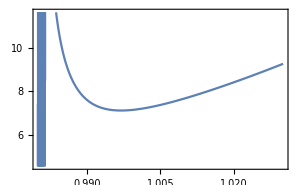

```mathematica
I0 = 0.0005;
S0 = 0.66;

ν0=1.01ν[I0, S0]
μ0=μ[I0, S0]
μf

Plot[T[v,μf,ν0,μ0],{v,0.98,1.03},
Frame-> True,
ImageSize->300
]


(*Manipulate[
Plot[T[v,μf,ν0,μ0],{v,1.06,1.2},
FrameLabel->{"v","T"},
Frame-> True
]
,{μ0,0.9466722766318828,3.3125850929940452}]*)
```

0.99

7.61105

1.99949

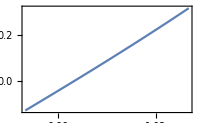

```mathematica
νf=0.99
T[νf,μf,ν0,μ0]

T0[νf,μ0,ν0,μ0]
```

```mathematica
datav=Table[
ν[Is,S]
,{S,0.1,1,0.1},{Is,0.1,1,0.1}];
MatrixPlot[datav,PlotLegends->Automatic]
{Min@datav,Max@datav}

datamu=Table[
μ[Is,S]
,{S,0.01,1,0.1},{Is,0.1,1,0.1}];
MatrixPlot[datamu,PlotLegends->Automatic]
{Min@datamu,Max@datamu}
```

-Graphics-

{1.06736,2.82694}

-Graphics-

{0.946672,3.31259}

0.856574

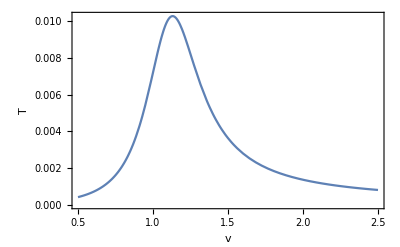

```mathematica
I0 = 0.0005;
S0 = 0.6;

ν0=1.01ν[I0, S0];
μ0=μ[I0, S0];

μf = Imax + (Log[R0]+1)/R0

Plot[Tc[v,μf,v,μ0],{v,0.5,2.5},
FrameLabel->{"v","T"},
Frame-> True
]
```

```mathematica
Manipulate[
(*ν0=0.7;*)
(*μ0=0.8;*)
Plot[T[v,μf,ν0,μ0],{v,0.7,1.03},
FrameLabel->{"v","T"},
Frame-> True
]
,{ν0,0.7,0.9},{μ0,0.8,1}]
```

```mathematica
Plot3D[T[v,μf,ν0,μ0],{v,0.98,1.03},{μ0,0.7,1.1}]
```

$Aborted

```mathematica
datamu=Table[
μ[Is,S]
,{S,0.01,1,0.1},{Is,0.1,1,0.1}]
```

## u_max=0.6

## Coloring the plane

```mathematica
Imax = 0.1;
R0 = 3.64;
umax = 0.6;
Rc = (1-umax)R0;

(*R0 = 2;
Rc = 4/3;

Imax = 0.01;*)
```

Formulas for the transition times

```mathematica
μ[S_,Is_]:=Is-1/R0 Log[S]+S
ν[S_,Is_]:=Is-1/Rc Log[S]+S

Ss[v_,mu_]:=Exp[(R0 Rc)/(R0 - Rc)(mu-v)]

Is[v_,mu_]:=R0/(R0 - Rc) mu - Rc/(R0 - Rc) v -Exp[(R0 Rc)/(R0 - Rc)(mu-v)]

(*hatSmu[mu_]:=-ProductLog[-ⅇ^(-R0 mu) R0]/R0
hatSnu[nu_]:=-ProductLog[-ⅇ^(-Rc nu) Rc]/Rc*)

hatSmu[mu_]:=Module[{S,sols},
sols=NSolve[mu==-1/R0 Log[S]+S, S,Reals];
Max[S/.sols]
]

hatSnu[nu_]:=Module[{S,sols},
sols=NSolve[nu==-1/Rc Log[S]+S, S,Reals];
Max[S/.sols]
]

muf = Imax + (Log[R0]+1)/R0
vmin = -1/Rc Log[hatSmu[muf ]]+hatSmu[muf ]

mumax=-1/R0 Log[hatSnu[vmin ]]+hatSnu[vmin ]
vmax = Imax + Log[R0]/Rc+1/R0



T0[ν1_,μ1_,ν0_,μ0_]:=NIntegrate[1/(R0/Rc μ0-v-(R0-Rc)/Rc Exp[(R0 Rc)/(R0-Rc)(μ0-v)]),{v,ν0,ν1}, Method->"LocalAdaptive",MaxRecursion->100]
Tc[ν1_,μ1_,ν0_,μ0_]:=NIntegrate[1/(-μ+Rc/R0 ν1+(R0-Rc)/R0 Exp[(R0 Rc)/(R0-Rc)(μ-ν1)]),{μ,μ0,μ1},Method->"LocalAdaptive",MaxRecursion->100]

(*T0[ν1_,μ1_,ν0_,μ0_]:=NIntegrate[1/(R0/Rc μ0-v-(R0-Rc)/Rc Exp[(R0 Rc)/(R0-Rc)(μ0-v)]),{v,ν0,ν1}, MaxRecursion->100]
Tc[ν1_,μ1_,ν0_,μ0_]:=NIntegrate[1/(-μ+Rc/R0 ν1+(R0-Rc)/R0 Exp[(R0 Rc)/(R0-Rc)(μ-ν1)]),{μ,μ0,μ1},MaxRecursion->100]*)

T[νf_?NumericQ,μf_?NumericQ,ν0_?NumericQ,μ0_?NumericQ]:=T0[νf,μ0,ν0,μ0]+Tc[νf,μf,νf,μ0]

(*T0[1.5,1.2,ν0,μ0]
Tc[1.5,1.2,ν0,μ0]
T[1.5,1.2,ν0,μ0]*)
```

0.729666

0.95412

0.865225

1.26208

```mathematica
vmin
vmax

muf
mumax
```

0.95412

1.26208

0.729666

0.865225

Switching surfaces

```mathematica
Phi[S_,R_]:=Module[{},
If[S≤ 1/R, Imax, Imax + 1/R(Log[R S]+1 - R S)]
]
```

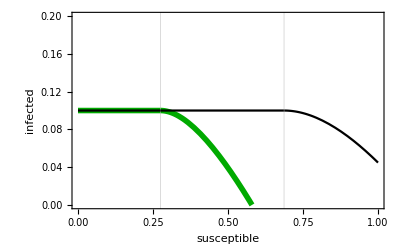

```mathematica
fig1=Show[
Plot[Phi[S, R0],{S, 0,1},
PlotRange->{{0,1},{0, 2 Imax}},
GridLines->{{1/R0,1/Rc},{}},
FrameTicks->{{Automatic,None},{Automatic,None}},
PlotStyle->Directive[Darker@Green,Thickness[0.01]],
FrameLabel->{"susceptible","infected"},
Frame->True
]
,
Plot[Phi[S, Rc],{S, 0,1},
PlotStyle->Black,
PlotRange->All]
]
```

```mathematica
I0 = 1*^-2//N
S0 = 1-I0//N

(*v0 = ν[S0, I0]*)
v0 = Mean[{vmin,vmax}]

munudata=ParallelTable[
{μ0,vf/.Last@NMinimize[{Evaluate@T[vf,muf,vmin,μ0],vmin≤ vf ≤ vmax},vf]}
,{μ0,muf,mumax,(mumax-muf)/10}];

Psi={Ss[#⟦2⟧,#⟦1⟧],Is[#⟦2⟧,#⟦1⟧]}&/@munudata
```

0.01

0.99

1.1081

{{0.56029,0.0102271},{0.554391,0.0267745},{0.533972,0.0504396},{0.517845,0.0716974},{0.505279,0.0910707},{0.495694,0.10895},{0.488623,0.12563},{0.483693,0.14133},{0.480599,0.156217},{0.479096,0.170416},{0.389447,0.216705}}

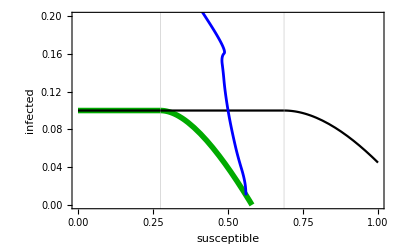

```mathematica
Show[
fig1
,
ListPlot[Psi,
Joined->True,
PlotStyle->{Blue, Thickness[0.005]},
InterpolationOrder->2]
,
PlotRange-> {All, {0,0.2}}
]
```

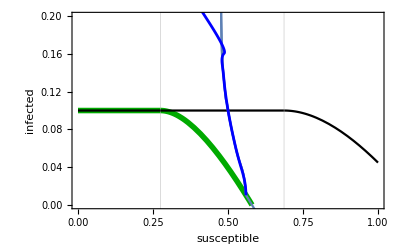

```mathematica
Psifun=Interpolation[Psi,InterpolationOrder->5];

Psifun2[S_?NumericQ]:=Module[{psivalue},
Which [
S <  Min[First@#&/@Psi], psivalue = 1,
S> Max[First@#&/@Psi], psivalue = Phi[S,R0],
True, psivalue = Psifun[S]
];
psivalue
]

Show[
fig1
,
Plot[Psifun[S],{S,Min[First@#&/@Psi], Max[First@#&/@Psi]}]
,
Plot[Psifun2[S],{S,0,1}]
,
ListPlot[Psi,
Joined->True,
PlotStyle->{Blue, Thickness[0.005]},
InterpolationOrder->2]
,
PlotRange-> {All, {0,0.2}}
]
```

Calculate S*

```mathematica
temp=Table[
{S,Norm[Psifun2[S]-Imax]},
{S,Min[First@#&/@Psi],Max[First@#&/@Psi],(Max[First@#&/@Psi]-Min[First@#&/@Psi])/1000}];
indx=Flatten@Position[temp⟦All,2⟧,Min@temp⟦All,2⟧]
Sstar=temp⟦indx, 1⟧⟦1⟧
```

{648}

0.499983

Color the (S,I) plane

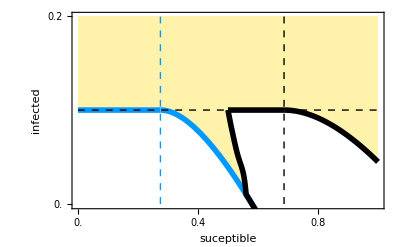

```mathematica
ϵ=0.7*^-3;

optimalcontrol[S_,Is_]:=Module[{uopt},
uopt=Which[
Is≤ Phi[S, R0], 0,
Is≥  Phi[S,Rc],umax,
Is≥ Phi[S, R0]&& Is≤ Psifun2[S],umax,
(*S≥ Sstar && S ≤ 1/Rc, 1-1/(β S),*)
True,0
];
uopt
]

optimalcontrol2[S_,Is_]:=Module[{uopt},
uopt=Which[
Is< Phi[S, R0]+ϵ, 0,
Is> Phi[S,Rc]+ϵ,umax,
Phi[S,Rc]-ϵ≤ Is≤  Phi[S,Rc]+ϵ && S≥ Sstar,(1/ϵ)(Is- Phi[S,Rc]),
(*Is<Phi[S,Rc]-ϵ,0,*)
(*Is == Phi[S, Rc], If[S≥ Sstar && S ≤ 1/Rc, 1-1/(β S), umax],*)
Is≥ Phi[S, R0]+ϵ&& Is≤ Psifun2[S] && S>1/R0,umax,
(*S≥ Sstar && S ≤ 1/Rc, 1-1/(β S),*)
True,0
];
uopt
]


figplane=Show[
DensityPlot[optimalcontrol[S,Is],{S,0,1},{Is,0,0.2}, 
(*ColorFunction->(Hue[0,2/3,1-#]&),*)
ColorFunction->(Blend[{White,RGBColor[1, 0.9500000000000001, 0.67]},#]&),
PlotPoints->100]
,
Plot[Phi[S, R0],{S, 0,1},
PlotStyle->Directive[RGBColor[0, 0.6, 1],Thickness[0.01]],
(*Filling->Bottom,*)
FillingStyle->Directive[RGBColor[0, 0.6, 1],Opacity[0.05]]
]
,
Plot[Phi[S, Rc],{S, Sstar,1},PlotStyle->Directive[Black,Thickness[0.01]]]
,
Plot[Psifun2[S],{S,Sstar,1},PlotStyle->Directive[Black,Thickness[0.01]]
]
,
Graphics[{RGBColor[0, 0.6, 1],Dashed,Line[{{1/R0,0},{1/R0,1}}]}]
,
Graphics[{Dashed,Line[{{1/Rc,0},{1/Rc,1}}]}]
,
Graphics[{Dashed,Line[{{0,Imax},{1,Imax}}]}]
,
PlotRange->{Automatic,{-0.001,0.2}},
FrameLabel->{Style["suceptible",13],Style["infected",13]},
FrameTicks->{{Range[0,1,0.05],None},{Range[0,1,0.2],None}},
AspectRatio->1/GoldenRatio
]
```

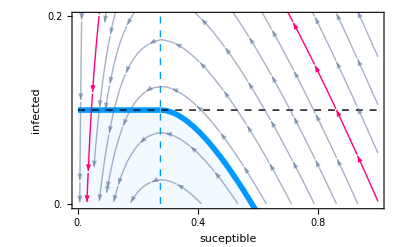

```mathematica
population = 8.855*^6;

Is0 =1/population;
S0 = 1-Is0;

Show[
Plot[Phi[S, R0],{S, 0,1},
PlotStyle->Directive[RGBColor[0, 0.6, 1],Thickness[0.01]],
Filling->Bottom,
FillingStyle->Directive[RGBColor[0, 0.6, 1],Opacity[0.05]]
]
,
Graphics[{RGBColor[0, 0.6, 1],Dashed,Line[{{1/R0,0},{1/R0,1}}]}]
,
Graphics[{Dashed,Line[{{0,Imax},{1,Imax}}]}]
,
StreamPlot[{-R0*Svar*Ivar, R0*Svar*Ivar - Ivar},{Svar,0,1},{Ivar, 0,1},
StreamPoints->{{{{0.99,0.01},RGBColor[1, 0, 0.5]},Automatic}},
StreamStyle->Directive[Opacity[0.5]]
]
,
PlotRange->{Automatic,{-0.001,0.2}},
Frame->True,
FrameLabel->{Style["suceptible",13],Style["infected",13]},
FrameTicks->{{Range[0,1,0.05],None},{Range[0,1,0.2],None}},
AspectRatio->1/GoldenRatio
]
```

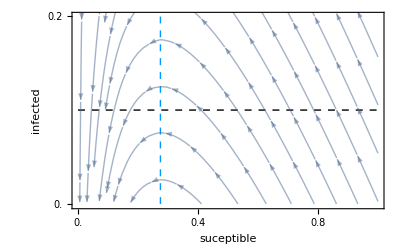

```mathematica
Show[
Plot[Phi[S, R0],{S, 0,1},
PlotStyle->Directive[RGBColor[0, 0.6, 1],Thickness[0.01],Opacity[0]],
Filling->Bottom,
FillingStyle->Directive[RGBColor[0, 0.6, 1],Opacity[0.05],Opacity[0]]
]
,
Graphics[{RGBColor[0, 0.6, 1],Dashed,Line[{{1/R0,0},{1/R0,1}}]}]
,
Graphics[{Dashed,Line[{{0,Imax},{1,Imax}}]}]
,
StreamPlot[{-R0*Svar*Ivar, R0*Svar*Ivar - Ivar},{Svar,0,1},{Ivar, 0,1},
StreamPoints->{{{{0.99,0.01},Automatic},Automatic}},
StreamStyle->Directive[Opacity[0.5]]
]
,
PlotRange->{Automatic,{-0.001,0.2}},
Frame->True,
FrameLabel->{Style["suceptible",13],Style["infected",13]},
FrameTicks->{{Range[0,1,0.05],None},{Range[0,1,0.2],None}},
AspectRatio->1/GoldenRatio
]
```

```mathematica
Pink
```

```mathematica
RGBColor[1, 0, 0.5]
```

## Simulation with optimal control

```mathematica
SolveSIRoptControl[I0_, S0_,γ_, β_,u_, tf_]:=Module[{s},
s=Flatten@NDSolve[{
S'[t]==-(1-u[S[t],Is[t]])β S[t]*Is[t],
Is'[t]==(1-u[S[t],Is[t]])β S[t]*Is[t]-γ Is[t],
S[0]==S0,Is[0]==I0},{S,Is},{t,tf},WorkingPrecision->10, MaxSteps->1*^8]
];

u0[S_,Is_]:=0

uopt[S_?NumericQ,Is_?NumericQ]:=Evaluate[optimalcontrol2[S,Is]]
```

```mathematica
Clear[SolveSIRoptControl]
```

```mathematica
tf = 120;

γ=1/7;
 β=0.52;

population = 8.855*^6;

Is0 =1/population;
S0 = 1-Is0;


s0opt = SolveSIRoptControl[Is0, S0,γ, β,uopt,tf ];
```

NDSolve::precw: The precision of the differential equation ({{S'[t]==0.52 Is[t] S[t] (-1+uopt[S[t],Is[t]]),Is'[t]==-Is[t]/7+0.52 Is[t] S[t] (1-uopt[«2»]),S[0]==1.,Is[0]==1.12931×10^-7},{},{},{},{}}) is less than WorkingPrecision (10.).

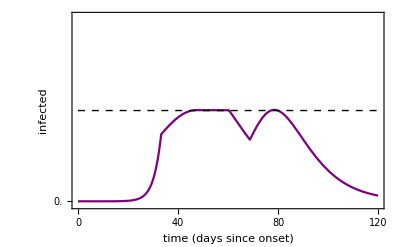

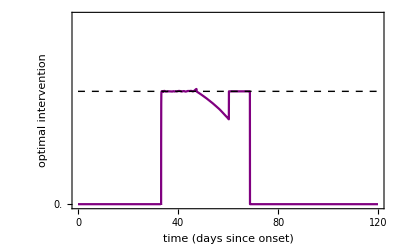

```mathematica
Show[
Plot[{
Evaluate[Is[t]/.s0opt]
},{t,0,tf},
Frame-> True,
PlotStyle->{
Directive[RGBColor[1, 0.25, 0.5]],
Directive[Darker@Red],
Directive[Purple]
},
PlotRange->{Automatic,{-0.004,0.204}},
FrameLabel->{Style["time (days since onset)",13],Style["infected",13]},
FrameTicks->{{Range[0,10,0.05],None},{Range[0,tf,20],None}},
AspectRatio->1/GoldenRatio,
ImageSize->{Automatic,230}
]
,
Graphics[{Dashed,Line[{{0,Imax},{tf,Imax}}]}]
]

Show[
Plot[{
Evaluate[uopt[S[t],Is[t]]/.s0opt]
},{t,0,tf},
Frame-> True,
PlotStyle->{
Directive[RGBColor[1, 0.25, 0.5]],
Directive[Darker@Red],
Directive[Purple]
},
PlotRange->{Automatic,{-0.004,1}},
FrameLabel->{Style["time (days since onset)",13],Style["optimal intervention",13]},
FrameTicks->{{Range[0,10,0.2],None},{Range[0,tf,20],None}},
AspectRatio->1/GoldenRatio,
ImageSize->{Automatic,230}
]
,
Graphics[{Dashed,Line[{{0,umax},{tf,umax}}]}]
]
```

```mathematica
tf = 120;

γ=1/7;
 β=0.52;

population = 8.855*^6;

Is0 =1/population;
S0 = 0.65;


s1opt = SolveSIRoptControl[Is0, S0,γ, β,uopt,tf ];
```

NDSolve::precw: The precision of the differential equation ({{S'[t]==0.52 Is[t] S[t] (-1+uopt[S[t],Is[t]]),Is'[t]==-Is[t]/7+0.52 Is[t] S[t] (1-uopt[«2»]),S[0]==0.65,Is[0]==1.12931×10^-7},{},{},{},{}}) is less than WorkingPrecision (10.).

```mathematica
tf = 120;

γ=1/7;
 β=0.52;

population = 8.855*^6;

Is0 =1/population;
S0 =0.8;


s2opt = SolveSIRoptControl[Is0, S0,γ, β,uopt,tf ];
```

NDSolve::precw: The precision of the differential equation ({{S'[t]==0.52 Is[t] S[t] (-1+uopt[S[t],Is[t]]),Is'[t]==-Is[t]/7+0.52 Is[t] S[t] (1-uopt[«2»]),S[0]==0.8,Is[0]==1.12931×10^-7},{},{},{},{}}) is less than WorkingPrecision (10.).

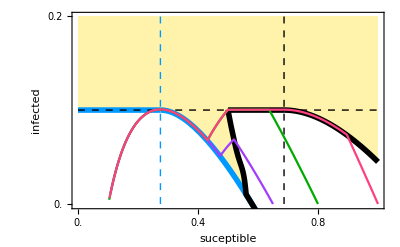

```mathematica
fig1=Show[
figplane
,
ParametricPlot[
Evaluate[{S[t],Is[t]}/.s1opt],{t,0,tf},
PlotStyle->Directive[RGBColor[0.63, 0.24, 0.99]]
]
,
ParametricPlot[
Evaluate[{S[t],Is[t]}/.s2opt],{t,0,tf},
PlotStyle->Directive[Darker@Green]
]
,
ParametricPlot[
Evaluate[{S[t],Is[t]}/.s0opt],{t,0,tf},
PlotStyle->Directive[RGBColor[1, 0.25, 0.5]]
]
,
ImageSize->{Automatic,230}
]
```

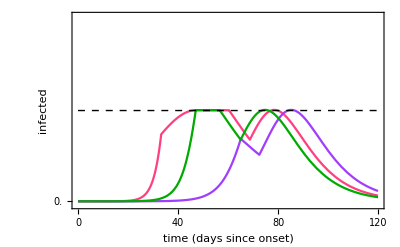

```mathematica
fig2=
Show[
Plot[{
Evaluate[Is[t]/.s0opt],
Evaluate[Is[t]/.s1opt],
Evaluate[Is[t]/.s2opt]
},{t,0,tf},
Frame-> True,
PlotStyle->{
Directive[RGBColor[1, 0.25, 0.5]],
Directive[RGBColor[0.63, 0.24, 0.99]],
Directive[Darker@Green]
},
PlotRange->{Automatic,{-0.004,0.204}},
FrameLabel->{Style["time (days since onset)",13],Style["infected",13]},
FrameTicks->{{Range[0,10,0.05],None},{Range[0,tf,20],None}},
AspectRatio->1/GoldenRatio,
ImageSize->{Automatic,230}
]
,
Graphics[{Dashed,Line[{{0,Imax},{tf,Imax}}]}]
]
```

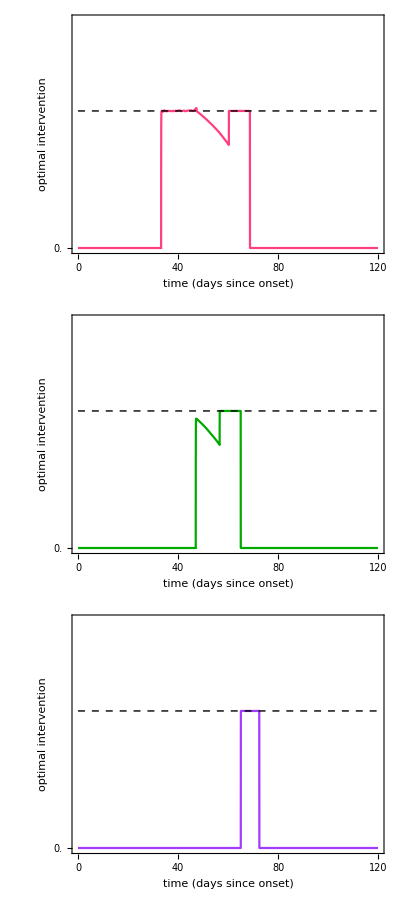

```mathematica
figu1=Show[
Plot[{
Evaluate[uopt[S[t],Is[t]]/.s0opt]
},{t,0,tf},
Frame-> True,
PlotStyle->{
Directive[RGBColor[1, 0.25, 0.5]]
},
PlotRange->{Automatic,{-0.004,1}},
FrameLabel->{Style["time (days since onset)",13],Style["optimal intervention",13]},
FrameTicks->{{Range[0,10,0.2],None},{Range[0,tf,20],None}},
AspectRatio->1/6GoldenRatio,
ImageSize->{340,Automatic}
]
,
Graphics[{Dashed,Line[{{0,umax},{tf,umax}}]}]
];

figu2=Show[
Plot[{
Evaluate[uopt[S[t],Is[t]]/.s2opt]
},{t,0,tf},
Frame-> True,
PlotStyle->{
Directive[Darker@Green]
},
PlotRange->{Automatic,{-0.004,1}},
FrameLabel->{Style["time (days since onset)",13],Style["optimal intervention",13]},
FrameTicks->{{Range[0,10,0.2],None},{Range[0,tf,20],None}},
AspectRatio->1/6GoldenRatio,
ImageSize->{340,Automatic}
]
,
Graphics[{Dashed,Line[{{0,umax},{tf,umax}}]}]
];

figu3=Show[
Plot[{
Evaluate[uopt[S[t],Is[t]]/.s1opt]
},{t,0,tf},
Frame-> True,
PlotStyle->{
Directive[RGBColor[0.63, 0.24, 0.99]]
},
PlotRange->{Automatic,{-0.004,1}},
FrameLabel->{Style["time (days since onset)",13],Style["optimal intervention",13]},
FrameTicks->{{Range[0,10,0.2],None},{Range[0,tf,20],None}},
AspectRatio->1/6GoldenRatio,
ImageSize->{340,Automatic}
]
,
Graphics[{Dashed,Line[{{0,umax},{tf,umax}}]}]
];

figu=Column[{figu1, figu2, figu3}, Spacings->-2]
```

```mathematica
Column[{fig1,"",fig2,"",figu}]
```

-Graphics-

-Graphics-

-Graphics-

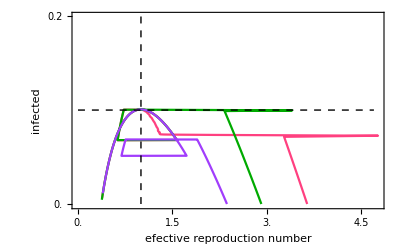

```mathematica
Show[
ParametricPlot[{
Evaluate[{R0 (1-uopt[S[t],Is[t]])S[t],Is[t]}/.s0opt],
Evaluate[{R0 (1-uopt[S[t],Is[t]])S[t],Is[t]}/.s2opt],
Evaluate[{R0 (1-uopt[S[t],Is[t]])S[t],Is[t]}/.s1opt]
},
{t,0,tf},
PlotStyle->{
Directive[RGBColor[1, 0.25, 0.5]],
Directive[Darker@Green],
Directive[RGBColor[0.63, 0.24, 0.99]]
},
GridLines->None,
Frame->True,
PlotRange->{All,{-0.001,0.2}},
FrameLabel->{Style["efective reproduction number",13],Style["infected",13]},
FrameTicks->{{Range[0,1,0.05],None},{Range[0,5,0.5],None}},
AspectRatio->1/GoldenRatio
]
,
Graphics[{Dashed,Line[{{1,0},{1,1}}]}]
,
Graphics[{Dashed,Line[{{0,Imax},{4.7,Imax}}]}]
]
```

```mathematica
ParametricPlot3D[{
Evaluate[{R0 (1-uopt[S[t],Is[t]])S[t],10*Is[t],uopt[S[t],Is[t]]}/.s0opt],
Evaluate[{R0 (1-uopt[S[t],Is[t]])S[t],10*Is[t],uopt[S[t],Is[t]]}/.s2opt],
Evaluate[{R0 (1-uopt[S[t],Is[t]])S[t],10*Is[t],uopt[S[t],Is[t]]}/.s1opt]
},{t,0,tf},
PlotRange->All,
AxesLabel->{Style["efective reproduction number",13],Style["infected",13], Style["input",13]},
PlotStyle->{
Directive[RGBColor[1, 0.25, 0.5]],
Directive[Darker@Green],
Directive[RGBColor[0.63, 0.24, 0.99]]
},
AspectRatio->1
]
```

-Graphics3D-

```mathematica
Show[
DensityPlot[optimalcontrol[S,Is],{S,0,1},{Is,0,0.2}, 
(*ColorFunction->(Hue[0,2/3,1-#]&),*)
ColorFunction->(Blend[{White,RGBColor[1, 0.9500000000000001, 0.67]},#]&),
PlotPoints->100]
,
Plot[Phi[S, R0],{S, 0,1},
PlotStyle->Directive[RGBColor[0, 0.6, 1],Thickness[0.01]],
(*Filling->Bottom,*)
FillingStyle->Directive[RGBColor[0, 0.6, 1],Opacity[0.05]]
]
,
Plot[Phi[S, Rc],{S, Sstar,1},PlotStyle->Directive[Black,Thickness[0.01]]]
,
Plot[Psifun2[S],{S,Sstar,1},PlotStyle->Directive[Black,Thickness[0.01]]
]
,
Graphics[{RGBColor[0, 0.6, 1],Dashed,Line[{{1/R0,0},{1/R0,1}}]}]
,
Graphics[{Dashed,Line[{{1/Rc,0},{1/Rc,1}}]}]
,
Graphics[{Dashed,Line[{{0,Imax},{1,Imax}}]}]
,
PlotRange->{Automatic,{-0.001,0.2}},
FrameLabel->{Style["suceptible",13],Style["infected",13]},
FrameTicks->{{Range[0,1,0.05],None},{Range[0,1,0.2],None}},
AspectRatio->1/GoldenRatio
]
```

-Graphics-

```mathematica
SfromRe[Re_,u_]:=Re/(R0*(1-u))
```

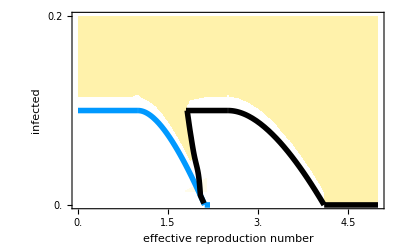

```mathematica
Show[
DensityPlot[optimalcontrol[SfromRe[Re,0],Is],{Re,0,5},{Is,0,0.2}, 
(*ColorFunction->(Hue[0,2/3,1-#]&),*)
ColorFunction->(Blend[{White,RGBColor[1, 0.9500000000000001, 0.67]},#]&),
PlotPoints->100]
,
Plot[Max[Phi[SfromRe[Re,0], R0],0],{Re, 0,2.2},
PlotStyle->Directive[RGBColor[0, 0.6, 1],Thickness[0.01]],
(*Filling->Bottom,*)
FillingStyle->Directive[RGBColor[0, 0.6, 1],Opacity[0.05]]
]
,
Plot[Max[0,Phi[SfromRe[Re,0], Rc]],{Re, 1.8,5},PlotStyle->Directive[Black,Thickness[0.01]]]
,
Plot[Max[0,Psifun2[SfromRe[Re,0]]],{Re,1.82,2.1},PlotStyle->Directive[Black,Thickness[0.01]]]
,
PlotRange->All,
FrameLabel->{Style["effective reproduction number",13],Style["infected",13]},
FrameTicks->{{Range[0,1,0.05],None},{Range[0,5,0.5],None}},
AspectRatio->1/GoldenRatio
]
```

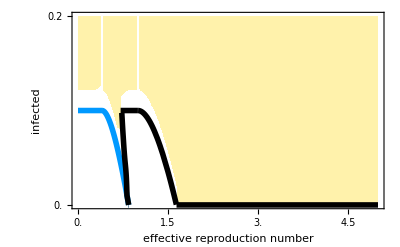

```mathematica
Show[
DensityPlot[optimalcontrol[SfromRe[Re,umax],Is],{Re,0,5},{Is,0,0.2}, 
(*ColorFunction->(Hue[0,2/3,1-#]&),*)
ColorFunction->(Blend[{White,RGBColor[1, 0.9500000000000001, 0.67]},#]&),
PlotPoints->10]
,
Plot[Max[Phi[SfromRe[Re,umax], R0],0],{Re, 0,0.85},
PlotStyle->Directive[RGBColor[0, 0.6, 1],Thickness[0.01]],
(*Filling->Bottom,*)
FillingStyle->Directive[RGBColor[0, 0.6, 1],Opacity[0.05]]
]
,
Plot[Max[0,Phi[SfromRe[Re,umax], Rc]],{Re, 0.71,5},PlotStyle->Directive[Black,Thickness[0.01]]]
,
Plot[Max[0,Psifun2[SfromRe[Re,umax]]],{Re,0.73,0.85},PlotStyle->Directive[Black,Thickness[0.01]]]
,
PlotRange->All,
FrameLabel->{Style["effective reproduction number",13],Style["infected",13]},
FrameTicks->{{Range[0,1,0.05],None},{Range[0,5,0.5],None}},
AspectRatio->1/GoldenRatio
]
```

## u_max=0.8

## Coloring the plane

```mathematica
Imax = 0.1;
R0 = 3.64;
umax = 0.8;
Rc = (1-umax)R0;

(*R0 = 2;
Rc = 4/3;

Imax = 0.01;*)
```

Formulas for the transition times

```mathematica
μ[S_,Is_]:=Is-1/R0 Log[S]+S
ν[S_,Is_]:=Is-1/Rc Log[S]+S

Ss[v_,mu_]:=Exp[(R0 Rc)/(R0 - Rc)(mu-v)]

Is[v_,mu_]:=R0/(R0 - Rc) mu - Rc/(R0 - Rc) v -Exp[(R0 Rc)/(R0 - Rc)(mu-v)]

(*hatSmu[mu_]:=-ProductLog[-ⅇ^(-R0 mu) R0]/R0
hatSnu[nu_]:=-ProductLog[-ⅇ^(-Rc nu) Rc]/Rc*)

hatSmu[mu_]:=Module[{S,sols},
sols=NSolve[mu==-1/R0 Log[S]+S, S,Reals];
Max[S/.sols]
]

hatSnu[nu_]:=Module[{S,sols},
sols=NSolve[nu==-1/Rc Log[S]+S, S,Reals];
Max[S/.sols]
]

muf = Imax + (Log[R0]+1)/R0
vmin = -1/Rc Log[hatSmu[muf ]]+hatSmu[muf ]

mumax=-1/R0 Log[hatSnu[vmin ]]+hatSnu[vmin ]
vmax = Imax + Log[R0]/Rc+1/R0



(*T0[ν1_,μ1_,ν0_,μ0_]:=NIntegrate[1/(R0/Rc μ0-v-(R0-Rc)/Rc Exp[(R0 Rc)/(R0-Rc)(μ0-v)]),{v,ν0,ν1}, Method->"LocalAdaptive",MaxRecursion->100]
Tc[ν1_,μ1_,ν0_,μ0_]:=NIntegrate[1/(-μ+Rc/R0 ν1+(R0-Rc)/R0 Exp[(R0 Rc)/(R0-Rc)(μ-ν1)]),{μ,μ0,μ1},Method->"LocalAdaptive",MaxRecursion->100]*)

T0[ν1_,μ1_,ν0_,μ0_]:=NIntegrate[1/(R0/Rc μ0-v-(R0-Rc)/Rc Exp[(R0 Rc)/(R0-Rc)(μ0-v)]),{v,ν0,ν1}]
Tc[ν1_,μ1_,ν0_,μ0_]:=NIntegrate[1/(-μ+Rc/R0 ν1+(R0-Rc)/R0 Exp[(R0 Rc)/(R0-Rc)(μ-ν1)]),{μ,μ0,μ1}]

T[νf_?NumericQ,μf_?NumericQ,ν0_?NumericQ,μ0_?NumericQ]:=T0[νf,μ0,ν0,μ0]+Tc[νf,μf,νf,μ0]

(*T0[1.5,1.2,ν0,μ0]
Tc[1.5,1.2,ν0,μ0]
T[1.5,1.2,ν0,μ0]*)
```

0.729666

1.32821

2.4135

2.14943

```mathematica
Clear[T]
```

```mathematica
vmin
vmax

muf
mumax
```

0.95412

1.26208

0.729666

0.865225

Switching surfaces

```mathematica
Phi[S_,R_]:=Module[{},
If[S≤ 1/R, Imax, Imax + 1/R(Log[R S]+1 - R S)]
]
```

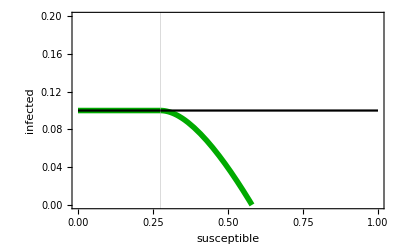

```mathematica
fig1=Show[
Plot[Phi[S, R0],{S, 0,1},
PlotRange->{{0,1},{0, 2 Imax}},
GridLines->{{1/R0,1/Rc},{}},
FrameTicks->{{Automatic,None},{Automatic,None}},
PlotStyle->Directive[Darker@Green,Thickness[0.01]],
FrameLabel->{"susceptible","infected"},
Frame->True
]
,
Plot[Phi[S, Rc],{S, 0,1},
PlotStyle->Black,
PlotRange->All]
]
```

```mathematica
muf
mumax

vmin
vmax
```

0.729666

2.4135

1.32821

2.14943

```mathematica
I0 = 1*^-2//N
S0 = 1-I0//N

(*v0 = ν[S0, I0]*)
v0 = Mean[{vmin,vmax}]

munudata=ParallelTable[
{μ0,vf/.Last@NMinimize[{Evaluate@T[vf,muf,vmin,μ0],vmin≤ vf ≤ vmax},vf]}
,{μ0,muf,mumax,(mumax-muf)/10}];

Psi={Ss[#⟦2⟧,#⟦1⟧],Is[#⟦2⟧,#⟦1⟧]}&/@munudata
```

0.01

0.99

1.73882

NIntegrate::zeroregion: Integration region {{1.32821,1.3282112602109568930473236137600659189887317137514759299400315821}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in v near {v} = {1.3282112602142321915391044810779937044284562954149335467501913399}. NIntegrate obtained 3.84182 and 0.0560301 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in v near {v} = {1.3282112608845255415588023285020269250843866215561206445272546262}. NIntegrate obtained 28.8295 and 0.253751 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in v near {v} = {1.3282112606624491906443835293153816776785987319176030041489866562}. NIntegrate obtained 3.79605 and 0.0296339 for the integral and error estimates.

NIntegrate::zeroregion: Integration region {{1.32821,1.3282112602109568664065029510791693594199239467959154604508304582}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in v near {v} = {1.3282112615015054495509025438259276570150853313823091639278572984}. NIntegrate obtained 3.89168 and 0.0427493 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in v near {v} = {1.3282112606624491906443835293153816776785987319176030041489866562}. NIntegrate obtained 28.6393 and 0.189535 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::zeroregion: Integration region {{1.32821,1.328211260210956812244376124001206097503562402010592759991243577}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

General::stop: Further output of NIntegrate::zeroregion will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in v near {v} = {1.3282112602109569484847006046427207126864165380520163579988084709}. NIntegrate obtained 29.4812 and 0.129532 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::inumri: The integrand 1/(3.64833-4. ⅇ^(0.91 (0.729666-v))-v) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{1.3282112602109568122443761240045935946314766921886793414572801416,1.3282112602109568122542196544428822576827399741574546730464310063}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

NMinimize::nnum: The function value NIntegrate[1/((R0 0.729666)/Rc-v-((R0+Times[«2»]) Exp[«3» Plus[«2»]])/Rc),{v,1.32821,1.52449}] is not a number at {vf} = {1.52449}.

{{0.432065,0.0670571},{0.430234,0.236105},{0.423122,0.407022},{0.451687,0.564788},{0.50709,0.709554},{0.59106,0.836064},{0.688935,0.948669},{0.803017,1.04507},{0.935991,1.12257},{1.09098,1.17806},{1.27792,1.20295}}

1.57158

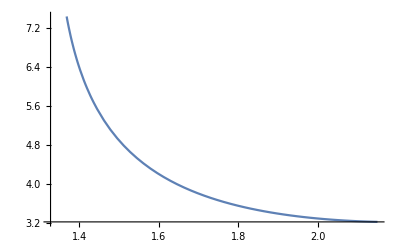

```mathematica
μ0= Mean[{muf,mumax}]
Plot[Evaluate@T[vf,muf,vmin,μ0],{vf,vmin, vmax}]
```

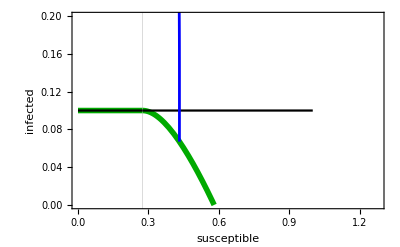

```mathematica
Show[
fig1
,
ListPlot[Psi,
Joined->True,
PlotStyle->{Blue, Thickness[0.005]},
InterpolationOrder->2]
,
PlotRange-> {All, {0,0.2}}
]
```

InterpolatingFunction[…]

InterpolatingFunction::dmval: Input value {0.0000245143} lies outside the range of data in the interpolating function. Extrapolation will be used.

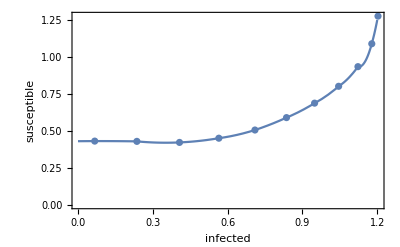

```mathematica
Psifun=Interpolation[{Last@#,First@#}&/@Psi,InterpolationOrder->2]

Show[
ListPlot[Interpolation[{Last@#,First@#}&/@Psi], 
FrameLabel->{"infected","susceptible"},
Frame->True]
,
Plot[Psifun[Is],{Is,0,1.2}]
]
```

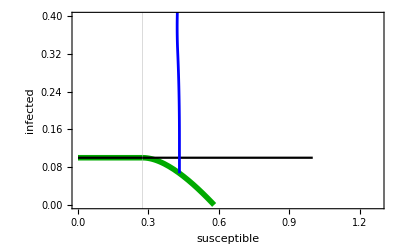

```mathematica
Psifun=Interpolation[Psi,InterpolationOrder->5];

Psifun2[S_?NumericQ]:=Module[{psivalue},
Which [
S <  Min[First@#&/@Psi], psivalue = 1,
S> Max[First@#&/@Psi], psivalue = Phi[S,R0],
True, psivalue = Psifun[S]
];
psivalue
]

Show[
fig1
,
Plot[Psifun[S],{S,Min[First@#&/@Psi], Max[First@#&/@Psi]}]
,
Plot[Psifun2[S],{S,0,1}]
,
ListPlot[Psi,
Joined->True,
PlotStyle->{Blue, Thickness[0.005]},
InterpolationOrder->2]
,
PlotRange-> {All, {0,0.4}}
]
```

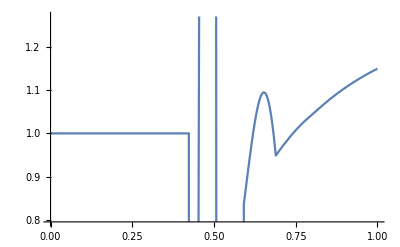

```mathematica
Plot[Psifun2[S],{S,0,1}]
```

InterpolatingFunction[…]

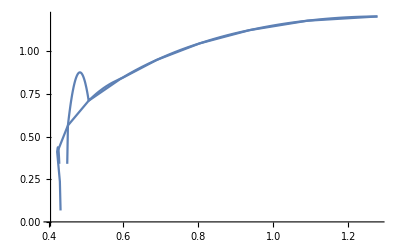

```mathematica
Psifun=Interpolation[Psi,InterpolationOrder->2,  Method->"Hermite"]

Psifun2[S_?NumericQ]:=Module[{psivalue},
Which [
S <  Min[First@#&/@Psi], psivalue = 1,
S> Max[First@#&/@Psi], psivalue = Phi[S,R0],
True, psivalue = Psifun[S]
];
psivalue
]

Show[
ListPlot[Psi,Joined->True]
,
Plot[Psifun[S],{S,Min[First@#&/@Psi], Max[First@#&/@Psi]}]
]
```

```mathematica
Psifun[0.6]
```

InterpolatingFunction[…][0.6]

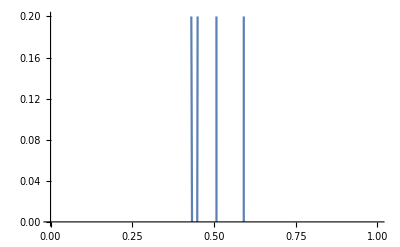

```mathematica
Plot[Psifun[S],{S,Min[First@#&/@Psi], Max[First@#&/@Psi]},PlotRange-> {{0,1}, {0,0.2}}]
```

Calculate S*

```mathematica
temp=Table[
{S,Norm[Psifun2[S]-Imax]},
{S,Min[First@#&/@Psi],Max[First@#&/@Psi],(Max[First@#&/@Psi]-Min[First@#&/@Psi])/1000}];
indx=Flatten@Position[temp⟦All,2⟧,Min@temp⟦All,2⟧]
Sstar=temp⟦indx, 1⟧⟦1⟧
```

{11}

0.43167

Color the (S,I) plane

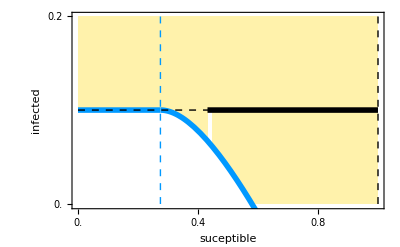

```mathematica
ϵ=0.7*^-3;

optimalcontrol[S_,Is_]:=Module[{uopt},
uopt=Which[
Is≤ Phi[S, R0], 0,
Is≥  Phi[S,Rc],umax,
Is≥ Phi[S, R0]&& Is≤ Psifun2[S],umax,
(*S≥ Sstar && S ≤ 1/Rc, 1-1/(β S),*)
True,0
];
uopt
]

optimalcontrol2[S_,Is_]:=Module[{uopt},
uopt=Which[
Is< Phi[S, R0]+ϵ, 0,
Is> Phi[S,Rc]+ϵ,umax,
Phi[S,Rc]-ϵ≤ Is≤  Phi[S,Rc]+ϵ && S≥ Sstar,(1/ϵ)(Is- Phi[S,Rc]),
(*Is<Phi[S,Rc]-ϵ,0,*)
(*Is == Phi[S, Rc], If[S≥ Sstar && S ≤ 1/Rc, 1-1/(β S), umax],*)
Is≥ Phi[S, R0]+ϵ&& Is≤ Psifun2[S] && S>1/R0,umax,
(*S≥ Sstar && S ≤ 1/Rc, 1-1/(β S),*)
True,0
];
uopt
]


figplane=Show[
DensityPlot[optimalcontrol[S,Is],{S,0,1},{Is,0,0.2}, 
(*ColorFunction->(Hue[0,2/3,1-#]&),*)
ColorFunction->(Blend[{White,RGBColor[1, 0.9500000000000001, 0.67]},#]&),
PlotPoints->100]
,
Plot[Phi[S, R0],{S, 0,1},
PlotStyle->Directive[RGBColor[0, 0.6, 1],Thickness[0.01]],
(*Filling->Bottom,*)
FillingStyle->Directive[RGBColor[0, 0.6, 1],Opacity[0.05]]
]
,
Plot[Phi[S, Rc],{S, Sstar,1},PlotStyle->Directive[Black,Thickness[0.01]]]
,
Plot[Psifun2[S],{S,Sstar,1},PlotStyle->Directive[Black,Thickness[0.01]]
]
,
Graphics[{RGBColor[0, 0.6, 1],Dashed,Line[{{1/R0,0},{1/R0,1}}]}]
,
Graphics[{Dashed,Line[{{Min[{1,1/Rc}],0},{Min[{1,1/Rc}],1}}]}]
,
Graphics[{Dashed,Line[{{0,Imax},{1,Imax}}]}]
,
PlotRange->{Automatic,{-0.001,0.2}},
FrameLabel->{Style["suceptible",13],Style["infected",13]},
FrameTicks->{{Range[0,1,0.05],None},{Range[0,1,0.2],None}},
AspectRatio->1/GoldenRatio
]
```

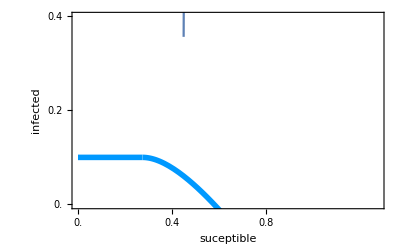

```mathematica
Show[
Plot[Psifun[S],{S,0.45, Max[First@#&/@Psi]}]
,
Plot[Phi[S, R0],{S, 0,1},
PlotStyle->Directive[RGBColor[0, 0.6, 1],Thickness[0.01]],
(*Filling->Bottom,*)
FillingStyle->Directive[RGBColor[0, 0.6, 1],Opacity[0.05]]
]
,
(*,
ListPlot[Psi,
Joined->True,
PlotStyle->{Blue, Thickness[0.005]},
InterpolationOrder->2]
,*)
Frame->True,
PlotRange->{Automatic,{-0.001,0.4}},
FrameLabel->{Style["suceptible",13],Style["infected",13]},
FrameTicks->{{Range[0,1,0.05],None},{Range[0,1,0.2],None}},
AspectRatio->1/GoldenRatio
]
```

## Simulation with optimal control

```mathematica
SolveSIRoptControl[I0_, S0_,γ_, β_,u_, tf_]:=Module[{s},
s=Flatten@NDSolve[{
S'[t]==-(1-u[S[t],Is[t]])β S[t]*Is[t],
Is'[t]==(1-u[S[t],Is[t]])β S[t]*Is[t]-γ Is[t],
S[0]==S0,Is[0]==I0},{S,Is},{t,tf},WorkingPrecision->10, MaxSteps->1*^8]
];

u0[S_,Is_]:=0

uopt[S_?NumericQ,Is_?NumericQ]:=Evaluate[optimalcontrol2[S,Is]]
```

```mathematica
Clear[SolveSIRoptControl]
```

```mathematica
tf = 120;

γ=1/7;
 β=0.52;

population = 8.855*^6;

Is0 =1/population;
S0 = 1-Is0;


s0opt = SolveSIRoptControl[Is0, S0,γ, β,uopt,tf ];
```

NDSolve::precw: The precision of the differential equation ({{S'[t]==0.52 Is[t] S[t] (-1+uopt[S[t],Is[t]]),Is'[t]==-Is[t]/7+0.52 Is[t] S[t] (1-uopt[«2»]),S[0]==1.,Is[0]==1.12931×10^-7},{},{},{},{}}) is less than WorkingPrecision (10.).

```mathematica
Show[
Plot[{
Evaluate[Is[t]/.s0opt]
},{t,0,tf},
Frame-> True,
PlotStyle->{
Directive[RGBColor[1, 0.25, 0.5]],
Directive[Darker@Red],
Directive[Purple]
},
PlotRange->{Automatic,{-0.004,0.204}},
FrameLabel->{Style["time (days since onset)",13],Style["infected",13]},
FrameTicks->{{Range[0,10,0.05],None},{Range[0,tf,20],None}},
AspectRatio->1/GoldenRatio,
ImageSize->{Automatic,230}
]
,
Graphics[{Dashed,Line[{{0,Imax},{tf,Imax}}]}]
]

Show[
Plot[{
Evaluate[uopt[S[t],Is[t]]/.s0opt]
},{t,0,tf},
Frame-> True,
PlotStyle->{
Directive[RGBColor[1, 0.25, 0.5]],
Directive[Darker@Red],
Directive[Purple]
},
PlotRange->{Automatic,{-0.004,1}},
FrameLabel->{Style["time (days since onset)",13],Style["optimal intervention",13]},
FrameTicks->{{Range[0,10,0.2],None},{Range[0,tf,20],None}},
AspectRatio->1/GoldenRatio,
ImageSize->{Automatic,230}
]
,
Graphics[{Dashed,Line[{{0,umax},{tf,umax}}]}]
]
```

-Graphics-

-Graphics-

```mathematica
tf = 120;

γ=1/7;
 β=0.52;

population = 8.855*^6;

Is0 =1/population;
S0 = 0.65;


s1opt = SolveSIRoptControl[Is0, S0,γ, β,uopt,tf ];
```

NDSolve::precw: The precision of the differential equation ({{S'[t]==0.52 Is[t] S[t] (-1+uopt[S[t],Is[t]]),Is'[t]==-Is[t]/7+0.52 Is[t] S[t] (1-uopt[«2»]),S[0]==0.65,Is[0]==1.12931×10^-7},{},{},{},{}}) is less than WorkingPrecision (10.).

```mathematica
tf = 120;

γ=1/7;
 β=0.52;

population = 8.855*^6;

Is0 =1/population;
S0 =0.8;


s2opt = SolveSIRoptControl[Is0, S0,γ, β,uopt,tf ];
```

NDSolve::precw: The precision of the differential equation ({{S'[t]==0.52 Is[t] S[t] (-1+uopt[S[t],Is[t]]),Is'[t]==-Is[t]/7+0.52 Is[t] S[t] (1-uopt[«2»]),S[0]==0.8,Is[0]==1.12931×10^-7},{},{},{},{}}) is less than WorkingPrecision (10.).

```mathematica
fig1=Show[
figplane
,
ParametricPlot[
Evaluate[{S[t],Is[t]}/.s1opt],{t,0,tf},
PlotStyle->Directive[RGBColor[0.63, 0.24, 0.99]]
]
,
ParametricPlot[
Evaluate[{S[t],Is[t]}/.s2opt],{t,0,tf},
PlotStyle->Directive[Darker@Green]
]
,
ParametricPlot[
Evaluate[{S[t],Is[t]}/.s0opt],{t,0,tf},
PlotStyle->Directive[RGBColor[1, 0.25, 0.5]]
]
,
ImageSize->{Automatic,230}
]
```

-Graphics-

```mathematica
fig2=
Show[
Plot[{
Evaluate[Is[t]/.s0opt],
Evaluate[Is[t]/.s1opt],
Evaluate[Is[t]/.s2opt]
},{t,0,tf},
Frame-> True,
PlotStyle->{
Directive[RGBColor[1, 0.25, 0.5]],
Directive[RGBColor[0.63, 0.24, 0.99]],
Directive[Darker@Green]
},
PlotRange->{Automatic,{-0.004,0.204}},
FrameLabel->{Style["time (days since onset)",13],Style["infected",13]},
FrameTicks->{{Range[0,10,0.05],None},{Range[0,tf,20],None}},
AspectRatio->1/GoldenRatio,
ImageSize->{Automatic,230}
]
,
Graphics[{Dashed,Line[{{0,Imax},{tf,Imax}}]}]
]
```

-Graphics-

```mathematica
figu1=Show[
Plot[{
Evaluate[uopt[S[t],Is[t]]/.s0opt]
},{t,0,tf},
Frame-> True,
PlotStyle->{
Directive[RGBColor[1, 0.25, 0.5]]
},
PlotRange->{Automatic,{-0.004,1}},
FrameLabel->{Style["time (days since onset)",13],Style["optimal intervention",13]},
FrameTicks->{{Range[0,10,0.2],None},{Range[0,tf,20],None}},
AspectRatio->1/6GoldenRatio,
ImageSize->{340,Automatic}
]
,
Graphics[{Dashed,Line[{{0,umax},{tf,umax}}]}]
];

figu2=Show[
Plot[{
Evaluate[uopt[S[t],Is[t]]/.s2opt]
},{t,0,tf},
Frame-> True,
PlotStyle->{
Directive[Darker@Green]
},
PlotRange->{Automatic,{-0.004,1}},
FrameLabel->{Style["time (days since onset)",13],Style["optimal intervention",13]},
FrameTicks->{{Range[0,10,0.2],None},{Range[0,tf,20],None}},
AspectRatio->1/6GoldenRatio,
ImageSize->{340,Automatic}
]
,
Graphics[{Dashed,Line[{{0,umax},{tf,umax}}]}]
];

figu3=Show[
Plot[{
Evaluate[uopt[S[t],Is[t]]/.s1opt]
},{t,0,tf},
Frame-> True,
PlotStyle->{
Directive[RGBColor[0.63, 0.24, 0.99]]
},
PlotRange->{Automatic,{-0.004,1}},
FrameLabel->{Style["time (days since onset)",13],Style["optimal intervention",13]},
FrameTicks->{{Range[0,10,0.2],None},{Range[0,tf,20],None}},
AspectRatio->1/6GoldenRatio,
ImageSize->{340,Automatic}
]
,
Graphics[{Dashed,Line[{{0,umax},{tf,umax}}]}]
];

figu=Column[{figu1, figu2, figu3}, Spacings->-2]
```

-Graphics-

```mathematica
Column[{fig1,"",fig2,"",figu}]
```

-Graphics-

-Graphics-

-Graphics-

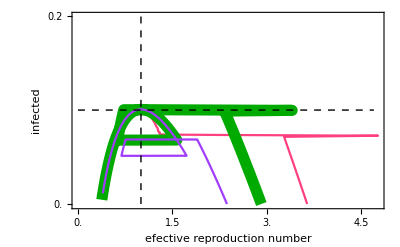

```mathematica
Show[
ParametricPlot[{
Evaluate[{R0 (1-uopt[S[t],Is[t]])S[t],Is[t]}/.s0opt],
Evaluate[{R0 (1-uopt[S[t],Is[t]])S[t],Is[t]}/.s2opt],
Evaluate[{R0 (1-uopt[S[t],Is[t]])S[t],Is[t]}/.s1opt]
},
{t,0,tf},
PlotStyle->{
Directive[RGBColor[1, 0.25, 0.5]],
Directive[Darker@Green, Thickness[0.02]],
Directive[RGBColor[0.63, 0.24, 0.99]]
},
GridLines->{{},{}},
Frame->True,
PlotRange->{All,{-0.001,0.2}},
FrameLabel->{Style["efective reproduction number",13],Style["infected",13]},
FrameTicks->{{Range[0,1,0.05],None},{Range[0,5,0.5],None}},
AspectRatio->1/GoldenRatio
]
,
Graphics[{Dashed,Line[{{1,0},{1,1}}]}]
,
Graphics[{Dashed,Line[{{0,Imax},{4.7,Imax}}]}]
]
```